### Chapter VI Fundamentals of the Wolfram Language

#### How MMA Computes

```mathematica
2 3+4 5 (*2 numbers are multiplied when there is a space between them*)
2 (3+4) 5
```

26

70

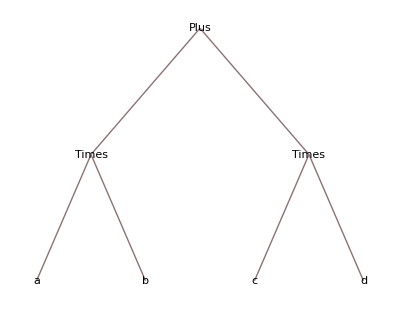

```mathematica
TreeForm[a b+c d]
```

```mathematica
x=10;
2^x
x==5
Clear[x]
```

1024

False

#### Creating Lists of values

```mathematica
Table[{i,i^2},{i,1,10,2}]
```

{{1,1},{3,9},{5,25},{7,49},{9,81}}

#### Mixing Text with calculations

MMA treats words as undefined values

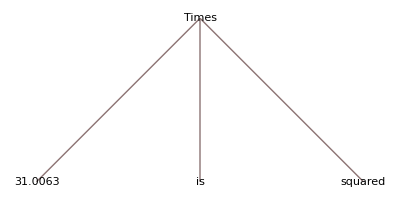

```mathematica
TreeForm[π squared is N[π^2]]
```

```mathematica
StringJoin["Frank","McFalane"]
"Frank"<>"McFalane" (*"<>" is a shortcut of string join*)
```

FrankMcFalane

FrankMcFalane

```mathematica
FullForm[N[π]]
FullForm[ToString[N[π]]]
```

3.14159

"3.14159"

#### Work with units

```mathematica
(10 m)/(5 s)*90 s (*Treat as undefined symbols*)
+ (*Using free form input*)
```

180 m

1504/127 ft

```mathematica
Quantity[2,"Feet"]+Quantity[3,"Meters"]
UnitConvert[%,"Meters"]
```

1504/127 ft

2256/625 m

```mathematica
Today
DatePlus[Today,{7,"Weeks"}]
```

Fri 23 Aug 2024

Fri 11 Oct 2024

```mathematica
DateList[DateObject[{2016,7,15,23,54,30}]]
```

{2016,7,15,23,54,30.}

#### Define Functions

```mathematica
f[x_]:=x^2+2x+3;
f[π]
f[{1,2,3}]
```

3+2 π+π^2

{6,11,18}

```mathematica
h[a_,b_]:=a^b
h[{1,2,3},{4,5,6}]
```

{1,32,729}

```mathematica
Function[x,x^2+2 x+3]
```

Function[x,x^2+2 x+3]

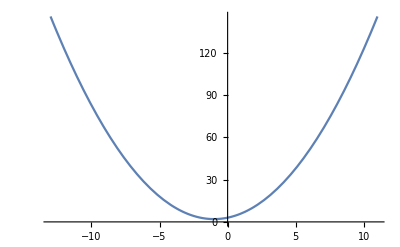

```mathematica
Plot[Function[x,x^2+2 x+3][x],{x,-13.,11.}]
```

```mathematica
Clear[x,a,b,f,h]
```

```mathematica
Plot3D[Function[{a,b},a^b][a,b],{a,0,1},{b,0,1}]
```

-Graphics3D-